### Manually integrate Schrodinger’s equation

The grid of x points in the region of the support of the potential

```mathematica
xgrid[p_]:=Module[{a,b,n,m, step,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n);

xs = Table[x,{x,a,b,step}]//N;

Return[xs];
]
```

The grid of x points in the entire region including some to the left of the support of the potential for determining the value of T.

```mathematica
xgridFull[p_]:=Module[{a,b,n,m, step,xs},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/(n);

xs = Table[x,{x,a-m*step,b,step}]//N;

Return[xs];
]
```

The H-matrix which for the linear system to determine psi(x)

```mathematica
Hmat[V_, k_, p_]:=Module[{xg, a,b,n,m, step,xs, diag, u1, u2, mat, u1V, matV},
xg=xgrid[p];
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];
step = (b-a)/n;

(*Some of these elements are constant and should not be recreated for every solution *)
diag = Band[{1,1}]->1;
u1 = Band[{1,2}]->2*(-1+step^2*k^2);
u2=Band[{1,3}]->1;
mat = SparseArray[{diag,u1,u2},{1+n+m, 1+n+m}];

(*These elements are constant for every value of k and should only be generated once per k value*)
(*u1V=Band[{1,2}]->(-2*step^2*V[xg]);
matV = SparseArray[u1V,{1+n+m,1+n+m}];*)

Return[mat];

];
```

The inhomogenous term for the linear system.

```mathematica
yvec[k_,p_]:=Module[{a,b,n,m, step,y},
a=p["a"];
b=p["b"];
n=p["n"];
m=p["m"];

step = (b-a)/n;

y =SparseArray[
{n+m+1->-Exp[I Sqrt[2]k step]+2(1-step^2 k^2),n+m->-1}, 
{n+m+1}];

Return[y];
]
```

Solve the linear system.

```mathematica
psiSoln[V_,k_,p_]:=
LinearSolve[Hmat[V,k,p],yvec[k,p],Method->"Banded"]
```

```mathematica
V[x_]:=1/Cosh[x]^2;
params = Association["a"->-5, "b"->5,"n"->1000,"m"->200];
```

```mathematica
psiTest = psiSoln[V,1.,params];
xGridFullTest = xgridFull[params];
psiTestofX=Table[{xGridFullTest[[i]],Re[psiTest[[i]]]},{i,1,Length[psiTest]}];
```

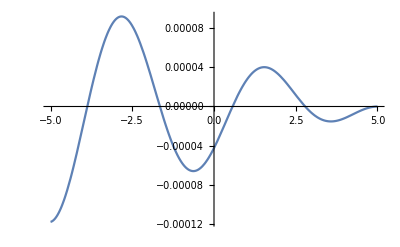

```mathematica
Plot[{Interpolation[psiTestofX][x]-Cos[Sqrt[2](x-5-10/1000)]},{x,-5,5}]
```